```mathematica
Id={{1,0},{0,1}};
sigX={{0,1},{1,0}};
sigY={{0,-I},{I,0}};
sigZ={{1,0},{0,-1}};
II=KroneckerProduct[Id,Id];
XX=KroneckerProduct[sigX,sigX];
IZ=KroneckerProduct[Id,sigZ];
IY=KroneckerProduct[Id,sigY];
IX=KroneckerProduct[Id,sigX];
XZ=KroneckerProduct[sigX,sigZ];
YY=KroneckerProduct[sigY,sigY];
ZZ=KroneckerProduct[sigZ,sigZ];
Phi00=1/2{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}};
Phi01=1/2{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}};
Phi10=1/2{{1,0,0,-1},{0,0,0,0},{0,0,0,0},{-1,0,0,1}};
Phi11=1/2{{0,0,0,0},{0,1,-1,0},{0,-1,1,0},{0,0,0,0}};
H=1/Sqrt[2]{{1,1},{1,-1}};
Hy=1/Sqrt[2]{{1,1},{-I,I}};
```

```mathematica
Clear[x,t]
```

```mathematica
v1=1/2{{Cos[x]},{Cos[x]},{Cos[x]},{Cos[x]}}+1/Sqrt[2]{{0},{Sin[x]},{-Sin[x]},{0}};
V1=KroneckerProduct[v1,Transpose[v1]];
v2=-1/2{{Sin[x]},{Sin[x]},{Sin[x]},{Sin[x]}}+1/Sqrt[2]{{0},{Cos[x]},{-Cos[x]},{0}};
V2=KroneckerProduct[v2,Transpose[v2]];
Simplify[Tr[V1]]
Simplify[V2.V1]
v={{Cos[x]},{Sin[x]},{Sin[x]},{Cos[x]}}/Sqrt[2];
V=KroneckerProduct[v,Transpose[v]];
```

```mathematica
x=Pi/4;
```

```mathematica
Xp=1/2{{1,1},{1,1}};
Xm=1/2{{1,-1},{-1,1}};
Yp=1/2{{1,I},{-I,1}};
Ym=1/2{{1,-I},{I,1}};
```

```mathematica
M1={{1,0},{0,Sqrt[1-t]}};
M2=Sqrt[t]{{0,1},{0,0}};
N1={{Sqrt[1-t],0},{0,1}};
N2=Sqrt[t]{{0,0},{1,0}};
ChA[X_]:=Transpose[N1].X.N1+Transpose[N2].X.N2
```

```mathematica
Simplify[Eigenvalues[ChA[Xp]]]
```

{1/2 (1-√(1-t)),1/2 (1+√(1-t))}

```mathematica
Simplify[ChAAD[II]]
```

{{√(1-t) Conjugate[√(1-t)]+√t Conjugate[√t],0,0,0},{0,1,0,0},{0,0,1-t+(-1+2 t) Conjugate[t]+2 √(-(-1+t) t) Conjugate[√(-(-1+t) t)],0},{0,0,0,√(1-t) Conjugate[√(1-t)]+√t Conjugate[√t]}}

```mathematica
ChAAFD[X_]:=Transpose[KroneckerProduct[M1,N1]].X.KroneckerProduct[M1,N1]+Transpose[KroneckerProduct[M1,N2]].X.KroneckerProduct[M1,N2]+Transpose[KroneckerProduct[M2,N1]].X.KroneckerProduct[M2,N1]+Transpose[KroneckerProduct[M2,N2]].X.KroneckerProduct[M2,N2]
```

```mathematica
Simplify[Eigenvalues[ChAAD[KroneckerProduct[Xp,Xm]]],t≥0]
```

{1/4 (2-2 √(1-t)-t),1/4 (2+2 √(1-t)-t),t/4,t/4}

```mathematica
Simplify[Eigenvalues[ChAAD[KroneckerProduct[Xp,Xm]]]]
```

{1/4 (2-2 √(1-t)-t),1/4 (2+2 √(1-t)-t),t/4,t/4}

```mathematica
Simplify[Eigenvalues[ChAAD[KroneckerProduct[Xm,Xm]]]]
```

{1/4 (2-2 √(1-t)-t),1/4 (2+2 √(1-t)-t),t/4,t/4}

```mathematica
Simplify[Eigenvalues[ChAAFD[Phi10]]]
```

{1-t,0,0,-(-1+t) t}

```mathematica
Simplify[Eigenvalues[ChAAFD[Phi11]],1>=t≥0]
```

{t/2,t/2,1/2 (1-t+t^2+(-1+t) √(1+t^2)),1/2 (1-t+t^2-(-1+t) √(1+t^2))}

```mathematica
Clear[t]
```

```mathematica
x=0.1;
```

```mathematica
t=.9
```

0.9

```mathematica
NMaximize[1/2 Root[-10 t^3+15 t^3 Cos[2 x]-6 t^3 Cos[4 x]+t^3 Cos[6 x]+(64 t-76 t^2+48 t^3+32 t Cos[2 x]-112 t^2 Cos[2 x]+32 t^3 Cos[2 x]+32 t Cos[4 x]-68 t^2 Cos[4 x]+48 t^3 Cos[4 x]) #1+(-64+16 t-16 t Cos[2 x]+64 t^2 Cos[2 x]) #1^2+32 #1^3&,2],{x}]
```

{0.45,{x→1.5708}}

```mathematica
Eigenvalues[ChAAFD[V]]
```

{1/4 (t-t Cos[2 x]),1/2 Root[-10 t^3+15 t^3 Cos[2 x]-6 t^3 Cos[4 x]+t^3 Cos[6 x]+(64 t-76 t^2+48 t^3+32 t Cos[2 x]-112 t^2 Cos[2 x]+32 t^3 Cos[2 x]+32 t Cos[4 x]-68 t^2 Cos[4 x]+48 t^3 Cos[4 x]) #1+(-64+16 t-16 t Cos[2 x]+64 t^2 Cos[2 x]) #1^2+32 #1^3&,1],1/2 Root[-10 t^3+15 t^3 Cos[2 x]-6 t^3 Cos[4 x]+t^3 Cos[6 x]+(64 t-76 t^2+48 t^3+32 t Cos[2 x]-112 t^2 Cos[2 x]+32 t^3 Cos[2 x]+32 t Cos[4 x]-68 t^2 Cos[4 x]+48 t^3 Cos[4 x]) #1+(-64+16 t-16 t Cos[2 x]+64 t^2 Cos[2 x]) #1^2+32 #1^3&,2],1/2 Root[-10 t^3+15 t^3 Cos[2 x]-6 t^3 Cos[4 x]+t^3 Cos[6 x]+(64 t-76 t^2+48 t^3+32 t Cos[2 x]-112 t^2 Cos[2 x]+32 t^3 Cos[2 x]+32 t Cos[4 x]-68 t^2 Cos[4 x]+48 t^3 Cos[4 x]) #1+(-64+16 t-16 t Cos[2 x]+64 t^2 Cos[2 x]) #1^2+32 #1^3&,3]}

```mathematica
NMaximize[Eigenvalues[ChAAFD[V],{x,t}]]
```

Eigenvalues::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in «1».

NMaximize::argbu: NMaximize called with 1 argument; between 2 and 4 arguments are expected.

NMaximize[Eigenvalues[{{1/2 (1-t) Cos[x]^2+1/2 t Sin[x]^2,1/2 √(1-t) Cos[x] Sin[x],1/2 (1-t)^(3/2) Cos[x] Sin[x]+1/2 √(1-t) t Cos[x] Sin[x],1/2 (1-t) Cos[x]^2},{1/2 √(1-t) Cos[x] Sin[x],Sin[x]^2/2,1/2 (1-t) Sin[x]^2,1/2 √(1-t) Cos[x] Sin[x]},{1/2 (1-t)^(3/2) Cos[x] Sin[x]+1/2 √(1-t) t Cos[x] Sin[x],1/2 (1-t) Sin[x]^2,(1-t) t Cos[x]^2+1/2 (1-t)^2 Sin[x]^2+1/2 t^2 Sin[x]^2,1/2 (1-t)^(3/2) Cos[x] Sin[x]+1/2 √(1-t) t Cos[x] Sin[x]},{1/2 (1-t) Cos[x]^2,1/2 √(1-t) Cos[x] Sin[x],1/2 (1-t)^(3/2) Cos[x] Sin[x]+1/2 √(1-t) t Cos[x] Sin[x],1/2 (1-t) Cos[x]^2+1/2 t Sin[x]^2}},{x,t}]]

```mathematica
Simplify[(-t-√(1+t^2))^2+1]
```

2 (1+t^2+t √(1+t^2))

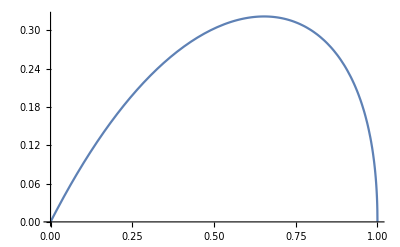

```mathematica
Plot[{1/2(2+2 √(1-t)-t)-1/2(1-t+t^2+√((-1+t)^2 (1+t^2)))-(1-t)},{t,0,1}]
```

```mathematica
Clear[x,t]
```

```mathematica
t=.95
```

0.95

```mathematica
x=0;
Eigenvalues[ChAAFD[V1]]
```

{0.05,0.0475,0.,0.}

```mathematica
x=0;
Eigenvalues[ChAAFD[V2]]
```

{0.510733,0.475,0.475,0.441767}

```mathematica
x=Pi/4;
Eigenvalues[ChAAFD[V1]]
```

{0.374303,0.2375,0.2375,0.150697}

```mathematica
x=Pi/4;
Eigenvalues[ChAAFD[V2]]
```

{0.374303,0.2375,0.2375,0.150697}

```mathematica
Max[Eigenvalues[ChAAFD[V1]]]+Max[Eigenvalues[ChAAFD[V2]]]
```

```mathematica
x=Pi/4;
t=.995;
Max[Eigenvalues[ChAAFD[V1]]]+Max[Eigenvalues[ChAAFD[V2]]]
```

0.573211

```mathematica
x=Pi/4+.25;
t=.995;
Max[Eigenvalues[ChAAFD[V1]]]+Max[Eigenvalues[ChAAFD[V2]]]
```

0.564609

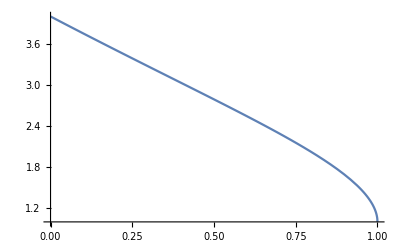

```mathematica
Plot[(1+Sqrt[1-t])^2-1/2 ((1-t)t),{t,0,1}]
```

```mathematica
Simplify[Tr[ChA[Xp].Xp]]
```

1/2 (1+√(1-t))

```mathematica
Simplify[Tr[ChA[Xp].Xp]]
```

1/2 (1+√(1-t))

```mathematica
Simplify[1/2Tr[sigX.ChA[sigX]]]
```

√(1-t)

```mathematica
Simplify[1/2Tr[sigX.ChA[sigZ]]]
```

0

```mathematica
Simplify[1/2Tr[sigX.ChA[sigZ]]]
```

-t/2

```mathematica
A={{Sqrt[1-t],0,0},{0,Sqrt[1-t],0},{-t/2,0,1-t/2}};
```

```mathematica
MatrixForm[A]
```

(√(1-t) | 0 | 0
0 | √(1-t) | 0
-t/2 | 0 | 1-t/2)

```mathematica
Eigenvalues[A.Transpose[A]]
```

{(2-t)/2,1-t,1/2 (2-3 t+t^2)}

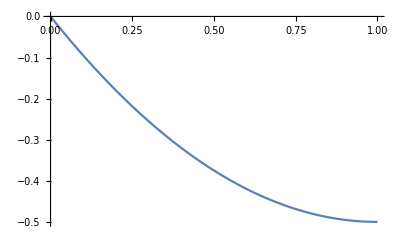

```mathematica
Plot[{1/2 (2-3 t+t^2)-(1-t/2)},{t,0,1}]
```

```mathematica
sx=a*Sqrt[1/2];
sy=0;
sz=a*Sqrt[1/2];
tx=a;
ty=0;
tz=a;
```

```mathematica
FullSimplify[Eigenvalues[II+sx*IX+sy*IY+sz*IZ+tx*XX+ty*YY+tz*ZZ],0≤a≤1]
```

{1+a-√2 a,1+(-1+√2) a,1-(1+√2) a,1+a+√2 a}

```mathematica
Solve[1+a-√2 a==0]
```

{{a→1/(-1+√2)}}

```mathematica
Solve[1-(1+√2) a==0]
```

{{a→1/(1+√2)}}

```mathematica
N[1/(1+√2)]
```

0.414214

```mathematica
sx=a/Sqrt[3];
sy=a/Sqrt[3];
sz=a/Sqrt[3];
tx=a/2;
ty=a/2;
tz=a/2;
```

```mathematica
FullSimplify[Eigenvalues[II+sx*IX+sy*IY+sz*IZ+tx*XX+ty*YY+tz*ZZ],0≤a≤1]
```

{1-a/2,1+(3 a)/2,1+(-1/2+√2) a,1-1/2 (1+2 √2) a}

```mathematica
Solve[1-1/2 (1+2 √2) a==0]
```

{{a→2/(1+2 √2)}}

```mathematica
sx=a/Sqrt[3];
sy=a/Sqrt[3];
sz=a/Sqrt[3];
tx=a/2;
ty=-a/2;
tz=a/2;
```

```mathematica
a=2/3;
```

```mathematica
FullSimplify[Eigensystem[II+sx*IX+sy*IY+sz*IZ+tx*XX+ty*YY+tz*ZZ],0≤a≤1]
```

{{2/3 (2+√2),4/3,-2/3 (-2+√2),0},{{-1+6/(3+√3-√6),((1+ⅈ) √3)/(3+√(21-6 √6)),-((1-ⅈ) √3)/(-3-3 √2+√3),1},{-1,((1+ⅈ) (-3+2 √3))/(-3+√3),-((1-ⅈ) √3)/(-3+√3),1},{-1+(-3+√3+√6)/(√2),-((1+ⅈ) √3)/(-3+3 √2+√3),-((1-ⅈ) √3)/(-3+3 √2+√3),1},{-1,((1+ⅈ) (3+2 √3))/(3+√3),-((1-ⅈ) √3)/(3+√3),1}}}

```mathematica
sx=Sqrt[(1+3b)(1-b)]/Sqrt[3];
sy=Sqrt[(1+3b)(1-b)]/Sqrt[3];
sz=Sqrt[(1+3b)(1-b)]/Sqrt[3];
tx=b;
ty=-b;
tz=b;
```

```mathematica
Clear[a,b]
```

```mathematica
FullSimplify[Eigenvalues[II+sx*IX+sy*IY+sz*IZ+tx*XX+ty*YY+tz*ZZ],0≤a≤1]
```

{0,2 (1+b),1-b-√(1+(2-3 b) b),1-b+√(1+(2-3 b) b)}

```mathematica
sx=a;
sy=a;
sz=a;
tx=b;
ty=-b;
tz=b;
```

```mathematica
FullSimplify[Eigenvalues[II+sx*IX+sy*IY+sz*IZ+tx*XX+ty*YY+tz*ZZ],0≤a≤1]
```

{1-√3 a-b,1+√3 a-b,1+b-√(3 a^2+4 b^2),1+b+√(3 a^2+4 b^2)}

```mathematica
Solve[1-b-√(1+(2-3 b) b)==0]
```

{{b→0},{b→1}}

```mathematica
Solve[1/2 (2+a-2 √2 a)==0]
```

{{a→2/(-1+2 √2)}}

```mathematica
N[2/(-1+2 √2)]
```

1.09384

```mathematica
N[2/(1+2 √2)]
```

0.522408

```mathematica
Solve[1-b-√(a^2+4 b^2)==0]
```

{{a→-√(1-2 b-3 b^2)},{a→√(1-2 b-3 b^2)}}

```mathematica
N[1/(1+Sqrt[2])]
```

0.414214

```mathematica
N[2/Sqrt[5]]
```

0.894427

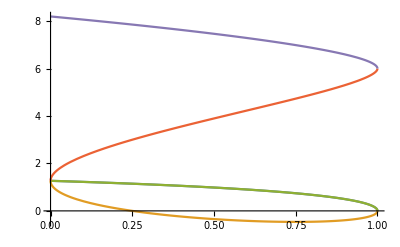

```mathematica
Plot[{3+√(3-3 a)-√3 √(4-a),3-√(3-3 a)-3 √a,(3+√(3-3 a)-√3 √(4-a)),(3-√(3-3 a)+3 √a), (3+√(3-3 a)+√3 √(4-a))},{a,0,1}]
```

```mathematica
Solve[3-√(3-3 a)-3 √a==0]
```

{{a→1/4},{a→1}}